# Mu3e sensitivity to low-mass boson

```mathematica
(*NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"madevent-analysis.nb"}]]*)
```

These will be set from the outside when called from analyze-all

```mathematica
(*rundir="run_300";
sig=FileNameJoin[{NotebookDirectory[],"..","muon-decay-newphysics","Events",rundir,"unweighted_events.lhe.gz"}];
bkg=FileNameJoin[{NotebookDirectory[],"..","muon-decay-background","Events",rundir,"unweighted_events.lhe.gz"}];*)
rawSig=Import[sig,"Table"];
rawBkg=Import[bkg,"Table"];
sigEvents=ReadME[rawSig];
bkgEvents=ReadME[rawBkg];
```

Define some useful functions

```mathematica
GetRate[raw_]:=
(
posStart=Position[raw,{"<init>"}][[1,1]];
posEnd=Position[raw,{"</init>"}][[1,1]];
DeleteCases[Take[raw,{posStart,posEnd}],{"<init>"}|{"</init>"}][[2,1]]*1
);

InvMass[event_,pair_]:=Sqrt[2*(enOf[event[[pair[[1]]]]]*enOf[event[[pair[[2]]]]]-ThreeVectorFrom[event[[pair[[1]]]]].ThreeVectorFrom[event[[pair[[2]]]]])];
ScaleData[bins_,counts_,scale_]:=
(
(* Note: scale must be an integer *)
Inner[ConstantArray, bins, scale*Append[counts, 0], Join]
)
```

The last event is just a set of headers, so we should ignore it with regards to our events.

```mathematica
Nsig=Length[sigEvents]-1;
Nbkg=Length[bkgEvents]-1;
(*EventPrint/@{sigEvents[[1]],bkgEvents[[1]]};*)
```

We are only really interested in the outgoing particles.

```mathematica
sigEvents=SetOut[sigEvents];
bkgEvents=SetOut[bkgEvents];
```

Construct the invariant masses of the electron-positron pairs.

```mathematica
firstPair=InvMass[#,{1,2}]&/@sigEvents[[1;;Nsig]];
secondPair=InvMass[#,{2,3}]&/@sigEvents[[1;;Nsig]];
sigInvMasses=Join[firstPair,secondPair];
sigRate=GetRate[rawSig];

firstPair=InvMass[#,{1,2}]&/@bkgEvents[[1;;Nbkg]];
secondPair=InvMass[#,{2,3}]&/@bkgEvents[[1;;Nbkg]];
bkgInvMasses=Join[firstPair,secondPair];
bkgRate=GetRate[rawBkg];
```

Define our bins

```mathematica
cutoff=10; (* MeV *)
Resolution[M_]:=0.004 Piecewise[{{cutoff, M≤cutoff}, {M, M>cutoff}}]
BinWidth[M_]:=2*Resolution[M]; (* Remove the Nyquist frequency *)
```

```mathematica
width=0;
bins=Reap[
While[width<100,
Sow[
width=BinWidth[width]+width
]
]][[2]][[1]];
bins=bins/1000;
```

Histograms of the invariant mass spectrum of e^+e^- pairs
Note: We don’t have the histograms properly weighted yet!

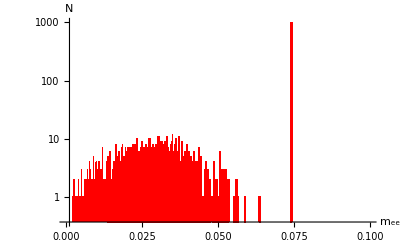

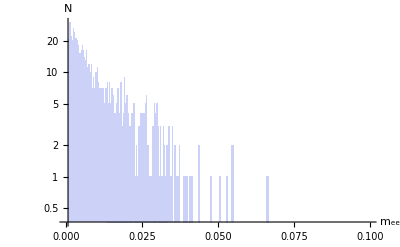

```mathematica
Histogram[sigInvMasses,{bins},ScalingFunctions->"Log",AxesLabel->{"m_ee","N"},ChartStyle->Red]
Histogram[bkgInvMasses,{bins},ScalingFunctions->"Log",AxesLabel->{"m_ee","N"}]
```

Compute the weight of each dataset

```mathematica
stopRate=2 10^9;
runTime=1;
Nstop=stopRate*runTime;
muonWidth=3.008/10^19;
sigBR=sigRate / (muonWidth+sigRate+bkgRate);
bkgBR=bkgRate/(muonWidth+sigRate+bkgRate);
sigScaling=Nstop*sigBR /Nsig;
bkgScaling=Nstop*bkgBR /Nbkg;
```

```mathematica
bkgScaling
sigScaling
```

2.61077×10^9

9.638

Get the histogram bin values so we can rescale as necessary.

```mathematica
{sigBins,sigCounts}=HistogramList[sigInvMasses,{bins},sigScaling*#2&];
{bkgBins,bkgCounts}=HistogramList[bkgInvMasses,{bins},bkgScaling*#2&];
sigCounts=Append[sigCounts,0.0]/2; (* There is one fewer counts than bins, and we double count our ee pairs *)
bkgCounts=Append[bkgCounts,0.0]/2;
```

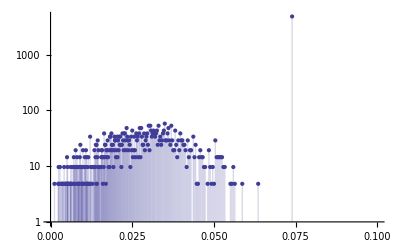

```mathematica
ListLogPlot[Transpose[{sigBins,sigCounts}],PlotRange->{{0,0.1},All},Filling->Axis]
```

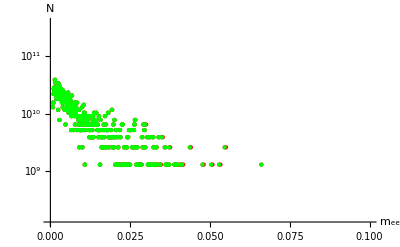

```mathematica
range={{0,0.1},{0.1*Min[DeleteCases[bkgCounts,0.0]],10*Max[bkgCounts]}};
ListLogPlot[{Transpose[{sigBins,sigCounts+bkgCounts}],Transpose[{bkgBins,bkgCounts}]},InterpolationOrder->0,PlotRange->range,PlotStyle->{Red,Green},Filling->{1->{2}},AxesLabel->{"m_ee","N"}]
```

Signal vs background computation

```mathematica
S=Total[sigCounts];
B=Total[bkgCounts];
sb=S/√B
```

0.00596489

Find if the number of signal events is larger than 3 statistical std. deviations of the background for any single bin

```mathematica
σ=√bkgCounts;
sigCounts;
3σ;
Or@@Flatten[Greater[#[[1]],#[[2]]]&/@Transpose[{sigCounts,3σ}]]
```

True